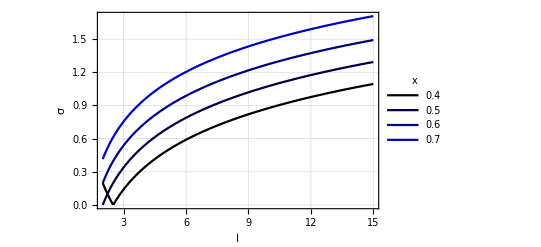

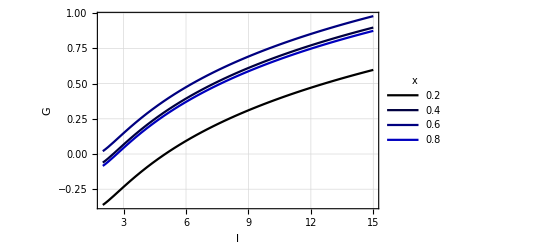

```mathematica
(*Volatility and Growth  as a function of space size with environmental and individual posterior as parameter*)
Clear[p];Clear[l];Clear[σ];
σ[p_,l_,x_]:=√((Log[(x(l-1))/(1-x)])^2 p(1-p))
G[p_,l_,x_]:=Log[l]+p Log[x ]+(1-p) Log[( (1-x))/(l-1)]
p=.6;
Plot[
Evaluate@Table[σ[p,l,x],{x,.4,.7,.1}],{l,2,15},
LabelStyle->Directive[FontFamily->"Times New Roman",FontSize->14],
PlotStyle->Table[
{RGBColor[0,0,a],Thick},
{a,.0,1,.25}],
Frame->True,
GridLines->Automatic,
FrameLabel->{"l","σ"},
PlotLegends->LineLegend[Table[x,{x,.4,.7,.1}],LegendLabel->x] 
]
Plot[
Evaluate@Table[G[p,l,x],{x,.2,.8,.2}],{l,2,15},
LabelStyle->Directive[FontFamily->"Times New Roman",FontSize->14],
PlotStyle->Table[
{RGBColor[0,0,a],Thick},
{a,.0,1,.25}],
Frame->True,
FrameLabel->{"l","G"},
PlotStyle->Thick,
GridLines->Automatic,
PlotLegends->LineLegend[Table[x,{x,.2,.8,.2}],LegendLabel->x]
]
```

```mathematica
Manipulate[
{Plot[√((Log[(x(l-1))/(1-x)])^2 x(1-x)),{x,0,1}],Plot[((1-x) x (1-x) ((-1+l)/(1-x)+((-1+l) x)/(1-x)^2) Log[((-1+l) x)/(1-x)])/((-1+l) x √((1-x) x Log[((-1+l) x)/(1-x)]^2)),{x,0,1},PlotRange->{-20,20}]}
,{l,2,50}]
```

~/Desktop/KellyVolPeak.pdf

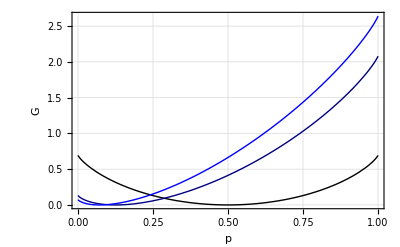

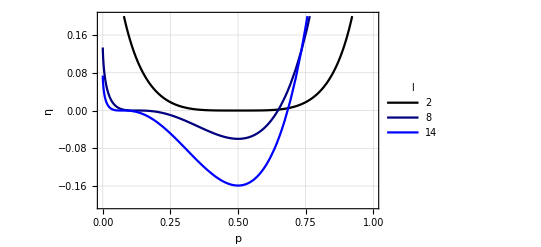

```mathematica
Clear[p];Clear[l];
Export["~/Desktop/KellyVolPeak.pdf",
Plot[
Evaluate@Table[σ[p,l,p],{l,2,15,6}],{p,0,1},
LabelStyle->Directive[FontFamily->"Times New Roman",FontSize->14],
PlotStyle->Table[
{RGBColor[0,0,a],Thick},
{a,.0,1,.5}],
Frame->True,
GridLines->Automatic,
FrameLabel->{"p","σ"}
]
]
(*Export["~/Desktop/KellyGPeak.pdf",*)
Plot[
Evaluate@Table[G[p,l,p],{l,2,15,6}],{p,0,1},
LabelStyle->Directive[FontFamily->"Times New Roman",FontSize->14],
PlotStyle->Table[
{RGBColor[0,0,a],Thick},
{a,.0,1,.5}],
Frame->True,
FrameLabel->{"p","G"},
PlotStyle->Thick,
GridLines->Automatic 
]
(*]*)
(*Export["~/Desktop/KellyEtaPeak.pdf",*)
Plot[
Evaluate@Table[G[p,l,p]-σ[p,l,p]^2/2,{l,2,15,6}],{p,0,1},
LabelStyle->Directive[FontFamily->"Times New Roman",FontSize->14],
PlotStyle->Table[
{RGBColor[0,0,a],Thick},
{a,.0,1,.5}],
Frame->True,
FrameLabel->{"p","η"},
PlotStyle->Thick,
GridLines->Automatic,
PlotRange->{-.2,.2},
PlotLegends->LineLegend[Table[l,{l,2,15,6}],LegendLabel->l] 
]
(*]*)
```

```mathematica
p=.7
Manipulate[
{Plot[√((Log[(x(l-1))/(1-x)])^2 p(1-p)),{x,0,1}],Plot[((1-p) p (1-x) ((-1+l)/(1-x)+((-1+l) x)/(1-x)^2) Log[((-1+l) x)/(1-x)])/((-1+l) x √((1-p) p Log[((-1+l) x)/(1-x)]^2)),{x,0,1},PlotRange->{-20,20}]}
,{l,2,50}]
```

0.7

```mathematica
Clear[p];Clear[l];
p=.7
Export["~/Desktop/KellySig.pdf",
Plot[
Evaluate@Table[σ[p,l,x],{l,2,10,3}],{x,0,1},
LabelStyle->Directive[FontFamily->"Times New Roman",FontSize->14],
PlotStyle->Table[
{RGBColor[a,0,0],Thick},
{a,.0,1,.5}],
Frame->True,
PlotRange->{0,1.15},
FrameLabel->{"x","σ"},
GridLines->{{1/2,1/5,1/8},None},
GridLinesStyle->Directive[Black,Dashed,Thick, Opacity[.5]]
]
]
Export["~/Desktop/KellyG.pdf",
Plot[
Evaluate@Table[G[p,l,x],{l,2,10,3}],{x,0,1},
LabelStyle->Directive[FontFamily->"Times New Roman",FontSize->14],
PlotStyle->Table[
{RGBColor[a,0,0],Thick},
{a,.0,1,.5}],
Frame->True,
PlotRange->{-1,1},
GridLines->{{.7},None},
GridLinesStyle->Directive[Black,Dashed,Thick, Opacity[.5]],
FrameLabel->{"x","γ"},
PlotStyle->Thick,
Epilog->{Text[Style["x_max=p",12,FontFamily->"Times New Roman",Italic],Scaled[{0.5,0.5}],{-2,8}],Red,Point@{.5,.5}}
]
]
Export["~/Desktop/KellyEta.pdf",
Plot[
Evaluate@Table[G[p,l,x]-σ[p,l,x]^2/2,{l,2,10,3}],{x,0,1},
LabelStyle->Directive[FontFamily->"Times New Roman",FontSize->14],
PlotStyle->Table[
{RGBColor[a,0,0],Thick},
{a,.0,1,.5}],
Frame->True,
FrameLabel->{"x","η"},
PlotStyle->Thick,
GridLines->Automatic,
PlotLegends->LineLegend[Table[l,{l,2,10,3}],LegendLabel->l] 
]
]
```

0.7

~/Desktop/KellySig.pdf

~/Desktop/KellyG.pdf

~/Desktop/KellyEta.pdf

```mathematica
LineLegend[Table[l,{l,2,15,6}],LegendLabel->l]
```

LineLegend[{2,8,14},LegendLabel→l]

```mathematica
Export["~/Desktop/LineLegend.pdf",
LineLegend[{Thick, {Thick,RGBColor[.5,0,0]}, {Thick,RGBColor[1,0,0]}},{"l=2","l=5","l=8"},LegendLayout->{"Row",1},
LabelStyle->Directive[FontFamily->"Times New Roman",FontSize->14,LegendLabel->"l"]]
]
```

~/Desktop/LineLegend.pdf

```mathematica
Clear[l];Clear[p];
Manipulate[
{Plot[
G[p,l,x],{x,0,1},
LabelStyle->Directive[FontFamily->"Times New Roman",FontSize->14],
PlotStyle->Table[
{RGBColor[a,0,0],Thick},
{a,.0,1,.5}],
Frame->True,
FrameLabel->{"x","G"},
PlotStyle->Thick,
GridLines->Automatic,
PlotRange->{-.1,.1}
],Plot[
σ[p,l,x],{x,0,1},
LabelStyle->Directive[FontFamily->"Times New Roman",FontSize->14],
PlotStyle->Table[
{RGBColor[a,0,0],Thick},
{a,.0,1,.5}],
Frame->True,
FrameLabel->{"x","G"},
PlotStyle->Thick,
GridLines->Automatic,
PlotRange->{-.1,.1}
]},{l,2,10},{p,0,1}]
```

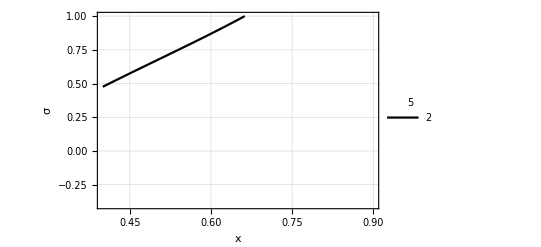

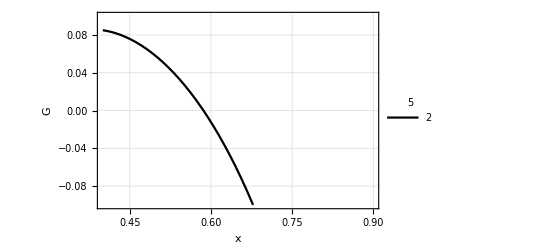

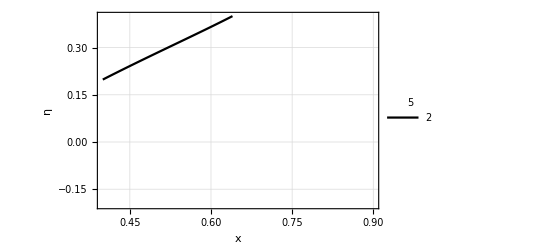

```mathematica
p=.38;
l=5;
Plot[
σ[p,l,x],{x,.4,.9},
LabelStyle->Directive[FontFamily->"Times New Roman",FontSize->14],
PlotStyle->Table[
{RGBColor[a,0,0],Thick},
{a,.0,1,.5}],
Frame->True,
FrameLabel->{"x","σ"},
PlotStyle->Thick,
GridLines->Automatic,
PlotRange->{-.4,1},
PlotLegends->LineLegend[Table[l,{l,2,15,6}],LegendLabel->l] 
]
Plot[
G[p,l,x],{x,.4,.9},
LabelStyle->Directive[FontFamily->"Times New Roman",FontSize->14],
PlotStyle->Table[
{RGBColor[a,0,0],Thick},
{a,.0,1,.5}],
Frame->True,
FrameLabel->{"x","G"},
PlotStyle->Thick,
GridLines->Automatic,
PlotRange->{-.1,.1},
PlotLegends->LineLegend[Table[l,{l,2,15,6}],LegendLabel->l] 
]
Plot[
G[p,l,x]+σ[p,l,x]^2/2,{x,.4,.9},
LabelStyle->Directive[FontFamily->"Times New Roman",FontSize->14],
PlotStyle->Table[
{RGBColor[a,0,0],Thick},
{a,.0,1,.5}],
Frame->True,
FrameLabel->{"x","η"},
PlotRange->{-.2,.4},
PlotStyle->Thick,
GridLines->Automatic,
PlotLegends->LineLegend[Table[l,{l,2,15,6}],LegendLabel->l] 
]
```

```mathematica
θ=1;
τ=1;
x0=5;
σ=.341;
```

```mathematica
Manipulate[Plot[
√(θ/(2 Pi σ^2/2(1-Exp[-2θ(t-τ)])))Exp[-θ/(2 σ^2/2)(x-x0 Exp[-θ(t-τ)])^2/(1-Exp[-2θ(t-τ)])],{x,0,10},
PlotRange->All]
,{t,.1,20}]
```

General::munfl: Exp[-1843.56] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-66363.4] is too small to represent as a normalized machine number; precision may be lost.

```mathematica
Clear[σ];Clear[θ];Clear[τ];Clear[x0];Clear[σ1];
Integrate[√(θ/(2 Pi σ^2/2(1-Exp[-2θ(t-τ)])))Exp[-θ/(2 σ^2/2)(x-x0 Exp[-θ(t-τ)])^2/(1-Exp[-2θ(t-τ)])]*1/(2Pi σ1)Exp[(-(x0-η)^2)/(2 σ1^2)],{x0,-Infinity,Infinity}]
```

ConditionalExpression[(ⅇ^(-((-2+ⅇ^(θ (t-τ)) x)^2 θ)/((-1+ⅇ^(2 θ (t-τ))) σ^2+2 θ σ1^2)) √(-θ/((-1+ⅇ^(2 θ (-t+τ))) σ^2)))/(√2 π √((2 θ)/((-1+ⅇ^(2 θ (t-τ))) σ^2)+1/σ1^2) σ1), Re[(2 θ)/((-1+ⅇ^(2 θ (t-τ))) σ^2)+1/σ1^2]≥0]

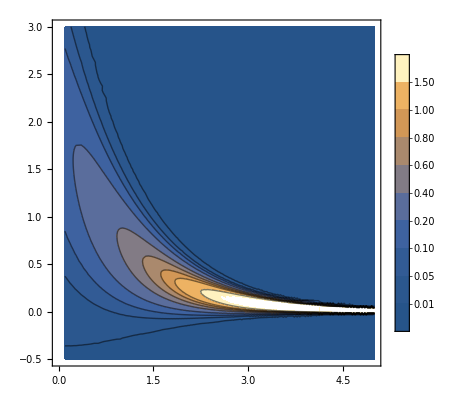

General::munfl: Exp[-1643.57] is too small to represent as a normalized machine number; precision may be lost.

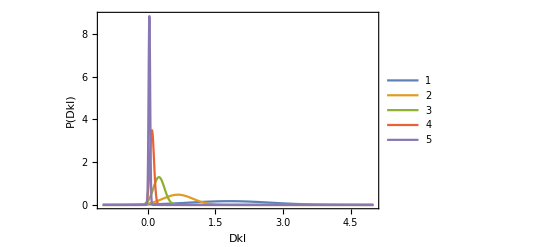

```mathematica
θ=1;
τ=0;
x0=6;
σ=.01;
σ1=1;
η=2;
ContourPlot[
(ⅇ^(-((ⅇ^(t θ) x-ⅇ^(θ τ) η)^2 θ)/(ⅇ^(2 t θ) σ^2-ⅇ^(2 θ τ) (σ^2-2 θ σ1^2))) √((θ (1+Coth[θ (t-τ)]))/σ^2))/(2 π σ1 √(1/σ1^2+(θ (-1+Coth[θ (t-τ)]))/σ^2)),{t,.1,5},{x,-.5,3},
PlotRange->{0,2},
Contours->{.01,.05,.1,.2,.4,.6,.8,1,1.5},
PlotLegends->Automatic,
Exclusions->None
]
Plot[Evaluate@Table[(ⅇ^(-((ⅇ^(t θ) x-ⅇ^(θ τ) η)^2 θ)/(ⅇ^(2 t θ) σ^2-ⅇ^(2 θ τ) (σ^2-2 θ σ1^2))) √((θ (1+Coth[θ (t-τ)]))/σ^2))/(2 π σ1 √(1/σ1^2+(θ (-1+Coth[θ (t-τ)]))/σ^2)),{t,.1,5,1}],{x,-1,5},PlotRange->All, Frame->True,PlotLegends->True,FrameLabel->{"Dkl","P(Dkl)"}]
```

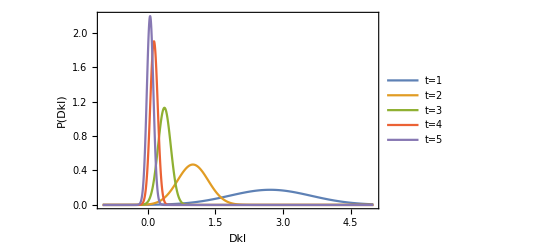

```mathematica
Clear[σ];Clear[θ];Clear[τ];Clear[x0];Clear[p];Clear[s];Clear[l];Clear[G]
```

```mathematica
FullSimplify[(ⅇ^(-((ⅇ^(t θ)-ⅇ^(θ τ))^2 x^2 θ)/(ⅇ^(2 t θ) σ^2-ⅇ^(2 θ τ) (σ^2-2 θ σ1^2))) √(-θ/((-1+ⅇ^(2 θ (-t+τ))) σ^2)))/(√2 π √((2 θ)/((-1+ⅇ^(2 θ (t-τ))) σ^2)+1/σ1^2) σ1)]
```

(ⅇ^(-((ⅇ^(t θ)-ⅇ^(θ τ))^2 x^2 θ)/(ⅇ^(2 t θ) σ^2-ⅇ^(2 θ τ) (σ^2-2 θ σ1^2))) √((θ (1+Coth[θ (t-τ)]))/σ^2))/(2 π σ1 √(1/σ1^2+(θ (-1+Coth[θ (t-τ)]))/σ^2))

```mathematica
Integrate[p+x/(1+t)1/(√(2 Pi s))Exp[(-(p Log[x]+(1-p)Log[(1-x)/(l-1)]-D0)^2)/(2 s^2)],{x,0,1}]
```

∫_0^1 (0.7+(ⅇ^(-(-D0+0.3 Log[1-x]+0.7 Log[x])^2/(2 s^2)) x)/(√(2 π) √s (1+t)))ⅆx

```mathematica
ConditionalExpression[(√(1/s^2) s^(3/2) (p+p t+x))/(1+t), Re[s^2]≥0]
```

```mathematica
p=.5
s=.1
x1=.3
Manipulate[
Plot[(√s (p+p t+x1))/(2 (1+t)),{x,0,1}],
{t,0,10}
]
```

0.5

0.1

0.3

```mathematica
FullSimplify[∫(p Log[1+x/p]+(1-p)Log[1+x/(1-p)])ⅆx]
```

-x+p (p+x) Log[(p+x)/p]+(-1+p) (-1+p-x) Log[1+x/(1-p)]

```mathematica
σ=.02;l=2;DD=.64;p=.7;G=.07;
Manipulate[
Plot[{1/(√(2 Pi)σ)(p/x+(1-p)/(1-x))Exp[-(Log[l]+p Log[p]+(1-p)Log[(1-p)/(l-1)]-p Log[p/x]-(1-p)Log[(1-p)/(1-x)]-(G))^2/(2 σ^2)],Log[l]+p Log[x]+(1-p)Log[(1-x)/(l-1)]},{x,0,1},PlotRange->{-1,60}],{G,-.1,.1}]
```

General::munfl: Exp[-57221.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-60073.8] is too small to represent as a normalized machine number; precision may be lost.

```mathematica
Log[2]
```

Log[2]

```mathematica
N[Log[2]]
```

0.693147

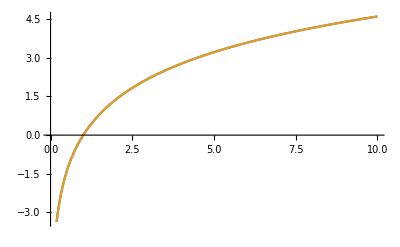

```mathematica
Plot[{Log[x]+Log[x],Log[x^2]},{x,0,10}]
```

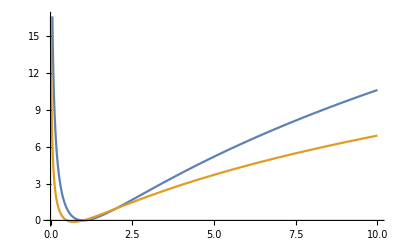

```mathematica
Plot[{Log[x]^2+Log[x]^2,Log[x]Log[2x]},{x,0,10}]
```

```mathematica
Plot[x,{x,0,1},Epilog->{Text[Style["hello",25],Scaled[{0.5,0.5}],#],Red,Point@{.5,.5}},PlotLabel->ToString@#]&/@{{-1,0},{1,0},{0,-1},{0,1}};
```

0.67

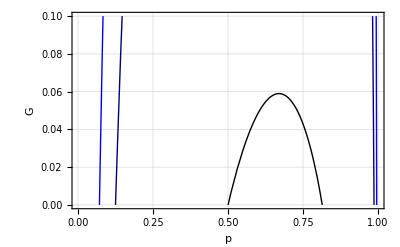

```mathematica
p=.67
Plot[
Evaluate@Table[G[p,l,x],{l,2,15,6}],{x,0,1},
LabelStyle->Directive[FontFamily->"Times New Roman",FontSize->14],
PlotStyle->Table[
{RGBColor[0,0,a],Thick},
{a,.0,1,.5}],
Frame->True,
FrameLabel->{"p","G"},
PlotStyle->Thick,
GridLines->Automatic, 
PlotRange->{0,.1}
]
```

```mathematica
p=.67
l=2
Manipulate[
Plot[
σ[p,l,p],
{p,0,1},
LabelStyle->Directive[FontFamily->"Times New Roman",FontSize->14],
PlotStyle->Table[
{RGBColor[0,0,a],Thick},
{a,.0,1,.5}],
Frame->True,
FrameLabel->{"x","G"},
PlotStyle->Thick,
GridLines->{{.7},None}
]
,{l,2,10}]
```

0.67

2

```mathematica
σ[.67,2,.67]^2/2
G[.67,2,.67]
```

0.0554437

0.0589685

```mathematica
G[.5,2,.5]
```

0.